# General Integration

This version uses a custom-written RK-4, state-space integrator instead of Mathematica's built-in integrator.

## The Beads

## Graphical Gadgets

```mathematica
torus[{R_, r_}, {x_,y_,z_}] :=(x^2+y^2+z^2+R^2-r^2)^2==4 R^2(x^2+z^2);
```

```mathematica
ring=ContourPlot3D[ 
Evaluate[torus[{1,.03},{x,y,z}]],
{x,-1.2,1.2},{y,-1.2,1.2},{z,-1.2,1.2},
Mesh->None,
ContourStyle->{RGBColor[1,.71,0],Specularity[White,10]},PlotPoints->100,Boxed->False,Axes->None];
```

```mathematica
frame=Graphics3D[{
Gray,Thick,Line[{
{{0,0,1},{0,0,1.2}},
{{-1.1,0,1.2},{1.1,0,1.2}},
{{0,0,-1},{0,0,-1.2}},
{{-1.1,0,-1.2},{1.1,0,-1.2}}}]}];
```

```mathematica
staticBall[θ_]:=Graphics3D[{
RGBColor[.33,.78,.26],Specularity[White,20],
Sphere[{
Sin[θ],(* Cos[Om a], *)
0,(* Sin[θ[t]/.sol[Om]],(* Sin[Om a], *)*)
-Cos[θ]},
.12]}];
```

```mathematica
ball[angfunc_,Om_,a_,rgb_:RGBColor[.33,.26,.78]]:= Graphics3D[{
rgb,Specularity[White,20],
Sphere[{
(* X *)Sin[angfunc[Om,a]],(* Cos[Om a], *)
(* Y *)0,(* Sin[angfunc[Om,a]],(* Sin[Om a], *)*)
(* Z *)-Cos[angfunc[Om,a]]},
(* r *).12]}];
```

```mathematica
ball2[{x_,y_},rgb_:RGBColor[.33,.26,.78]]:= Graphics3D[{
rgb,Specularity[White,20],Sphere[{x,y,0},(* r *).5]}];
```

```mathematica
ball2[{1,2},{RGBColor[1,2,3]}]
```

-Graphics3D-

```mathematica
minotaur[Om_,a_]:=Graphics3D[{
Text["θ = "<>ToString@theta[1,Om,a],{-.8,0,1}],
Text["θ̇ = "<>ToString@thetaDot[1,Om,a],{.8,0,1}]}];
```

```mathematica
minotaurRK[angFunc_,velFunc_,k_,Om_,a_]:=Graphics3D[{
Text["θ = "<>ToString@angFunc[k,Om,a],{-.8,0,1}],
Text["θ̇ = "<>ToString@velFunc[k,Om,a],{.8,0,1}]}];
```

## Parameters

### Permutations

```mathematica
preps[x_,lls_List]:=Map[
Function[l,Prepend[l,x]],
lls];
```

```mathematica
perms[{}]:={{}};
```

```mathematica
perms[l_List]:=Flatten[
Map[
Function[elt,preps[elt,perms[Complement[l,{elt}]]]],
l],1];
```

### Colors

```mathematica
greenCol=RGBColor[.33,.78,.26];
```

```mathematica
randCol:=RGBColor@@RandomReal[1,3];
```

```mathematica
col1=RGBColor@@RandomSample[{.33,.78,.26}];
```

```mathematica
col2=RGBColor@@RandomSample[{.33,.78,.26}];
```

```mathematica
col3=RGBColor@@RandomSample[{.33,.78,.26}];
```

```mathematica
col4=RGBColor@@RandomSample[{.33,.78,.26}];
```

```mathematica
col5=RGBColor@@RandomSample[{.33,.78,.26}];
```

```mathematica
col6=RGBColor@@RandomSample[{.33,.78,.26}];
```

```mathematica
col7=RGBColor@@RandomSample[{.33,.78,.26}];
```

### Global System Parameters

```mathematica
topΩ=9.6;
incrΩ=0.8;
```

```mathematica
Ωs=Table[i,{i,0,topΩ,incrΩ}]
```

{0.,0.8,1.6,2.4,3.2,4.,4.8,5.6,6.4,7.2,8.,8.8,9.6}

### Per-Bead Parameters

```mathematica
μ=2;
ϵ=0.001; (* unused at present *)
m=1;
R=1;
g=9.8;
lowT=0;
highT=20;
```

## Custom Integrator

Write differential equations in first-order, state-space form. In particular, Lagrange's equations (or Newton's) look like this

ⅆ/ⅆt[q(t)
q̇(t)]=[0 | 1
F(q,q̇,t) | G(q,q̇,t)][q(t)
q̇(t)]

In shorthand: Ψ(t)=[q(t),q̇(t)]^T, Φ(q,q̇,t)=[[0,1],[F(q,q̇,t),G(q,q̇,t)]], then

ⅆ/ⅆt Ψ(t)=Φ(q,q̇,t)Ψ(t)

For instance, consider a spring with constant -k and a damper with constant -ν on a mass m in one dimension. Write the equations as

[q̇(t)
q̈(t)]=[0 | 1
-k/m | -ν/m][q(t)
q̇(t)]

In general, as above, the derivative matrix is a function of the q-vector and of the time, but this one is constant

The following is a completely general, fourth-order Runge-Kutta integrator that takes four arguments:
	ψ: a state vector at any time
	ϕ: a function of ψ and t that returns a state-space matrix as above
	t: the current time
	dt: the interval of time to the next time

The derivative Ψ̇ is a linear approximation to the original function Ψ. To get an increment in Ψ, apply Ψ̇ to an increment dt in the input, that is, multiply Ψ̇ by dt because, for linear functions, application is multiplication.

To produce a sequence of integrands, just FoldList this over a Range of times, as shown immediately below:

```mathematica
rkStep[ψ_,ϕ_,t_,dt_]:=
Module[{dtk1=dt*ϕ[ψ,t].ψ},
Module[{dtk2=dt*ϕ[ψ+dtk1/2,t+dt/2].(ψ+dtk1/2)},
Module[{dtk3=dt*ϕ[ψ+dtk2/2,t+dt/2].(ψ+dtk2/2)},
Module[{dtk4=dt*ϕ[ψ+dtk3,t+dt].dtk3},
ψ+(dtk1+2dtk2+2dtk3+dtk4)/6]]]]
```

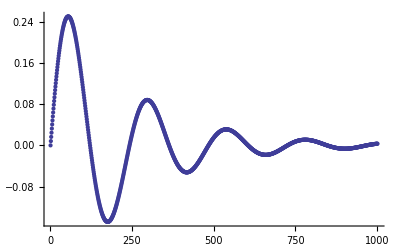

```mathematica
ListPlot[#⟦1⟧&/@
Module[{
m=1, (* mass *)
k=10, (* spring constant *)
ν=1, (* damping constant *)
dt=0.01, (* time step (ansatz) *)
t0=0, (* start time *)
tN=10, (* end time *)
mat, (* matrix in state-space form *)
ϕ}, (* function of q and t that returns a matrix in proper form *)
mat={{0,1},{-k/m,-ν/m}};
ϕ=Function[{ψ,t},mat];(* This time, it's a constant matrix ... *)
FoldList[
rkStep[#1,ϕ,#2,dt]&,(* calculate one step *)
{0,1},(* initial state *)
Range[t0,tN,dt]]]]
```

## Equations of Motion

### Gravitation, Spin, and Damping

```mathematica
gravf[ang_]:=-g m R Sin[ang]
```

```mathematica
spinf[ang_,Ω_]:=m R^2 Ω^2 Cos[ang] Sin[ang]
```

```mathematica
dampf[angVel_]:=-μ R angVel
```

### Electrostatic Repulsion

circumferential component of electrostatic force on thing at θ1 from thing at θ2. thetas have zero point at bottom of ring.

```mathematica
ef[θ1_,θ2_]:=Module[{
x=R Cos[#]&,y=R Sin[#]&,
ψ=θ2-θ1,dx,dy,
dsqrd,fmag,dir,compo,
c1=1,c2=1},
dx=x[θ2]-x[θ1];dy=y[θ2]-y[θ1];dsqrd=dx^2+dy^2;
fmag=c1 c2/dsqrd;
dir=ArcTan[1-Cos[ψ],-Sin[ψ]];
compo=fmag Sin[dir];
compo];
```

```mathematica
repulsef[ψ_,k_,n_]:=
-Sum[ef[ψ⟦i⟧,ψ⟦k⟧],{i,Complement[Range[n],{k}]}]
```

dampf is linear; leave it out of the following:

```mathematica
nonlinf[ψ_,k_,n_,Ω_]:=
gravf[ψ⟦k⟧]+spinf[ψ⟦k⟧,Ω]+repulsef[ψ,k,n]
```

### State-space for the Beads

Let the state of the seven beads on the wire be 7 thetas in a row, and their velocities be seven theta-dots in a row. The state vector [q,q̇], thus has 14 elements, and the state-space matrix is 14×14:

```mathematica
beadsMat[ψ_,Ω_,t_]:={
{0,0,0,0,0,0,0,1,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,1,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,1,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,1,0,0,0},
{0,0,0,0,0,0,0,0,0,0,0,1,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,1,0},
{0,0,0,0,0,0,0,0,0,0,0,0,0,1},{nonlinf[ψ,1,7,Ω]/(m R^2 ψ⟦1⟧),0,0,0,0,0,0,-μ R/(m R^2),0,0,0,0,0,0},
{0,nonlinf[ψ,2,7,Ω]/(m R^2 ψ⟦2⟧),0,0,0,0,0,0,-μ R/(m R^2),0,0,0,0,0},
{0,0,nonlinf[ψ,3,7,Ω]/(m R^2 ψ⟦3⟧),0,0,0,0,0,0,-μ R/(m R^2),0,0,0,0},
{0,0,0,nonlinf[ψ,4,7,Ω]/(m R^2 ψ⟦4⟧),0,0,0,0,0,0,-μ R/(m R^2),0,0,0},
{0,0,0,0,nonlinf[ψ,5,7,Ω]/(m R^2 ψ⟦5⟧),0,0,0,0,0,0,-μ R/(m R^2),0,0},
{0,0,0,0,0,nonlinf[ψ,6,7,Ω]/(m R^2 ψ⟦6⟧),0,0,0,0,0,0,-μ R/(m R^2),0},
{0,0,0,0,0,0,nonlinf[ψ,7,7,Ω]/(m R^2 ψ⟦7⟧),0,0,0,0,0,0,-μ R/(m R^2)}
}
```

```mathematica
ψlook={.1,.2, .3, .4, .5, .6, .7,0,0,0,0,0,0,0};
```

```mathematica
beadsMat[ψlook, 0, 0.4]
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
-1498.64 | 0 | 0 | 0 | 0 | 0 | 0 | -2 | 0 | 0 | 0 | 0 | 0 | 0
0 | -240.697 | 0 | 0 | 0 | 0 | 0 | 0 | -2 | 0 | 0 | 0 | 0 | 0
0 | 0 | -67.2432 | 0 | 0 | 0 | 0 | 0 | 0 | -2 | 0 | 0 | 0 | 0
0 | 0 | 0 | -9.54075 | 0 | 0 | 0 | 0 | 0 | 0 | -2 | 0 | 0 | 0
0 | 0 | 0 | 0 | 25.157 | 0 | 0 | 0 | 0 | 0 | 0 | -2 | 0 | 0
0 | 0 | 0 | 0 | 0 | 67.7649 | 0 | 0 | 0 | 0 | 0 | 0 | -2 | 0
0 | 0 | 0 | 0 | 0 | 0 | 203.675 | 0 | 0 | 0 | 0 | 0 | 0 | -2)

```mathematica
(Timing[soln=Module[{
dt=0.04, (* time step (ansatz) *)
t0=0, (* start time *)
tN=5, (* end time *)
ϕ}, (* function of q and t that returns a matrix in proper form *)
ϕ=Function[{q,t},beadsMat[q,0,t]];
FoldList[
rkStep[#1,ϕ,#2,dt]&,(* calculate one step *)
{RandomReal[2π],RandomReal[2π],RandomReal[2π],RandomReal[2π],RandomReal[2π],RandomReal[2π],RandomReal[2π],0,0,0,0,0,0,0},(* initial state *)
Range[t0,tN,dt]]]]⟦1⟧//ToString)<>" Seconds to solve."
```

1.716 Seconds to solve.

```mathematica
Length@soln
```

127

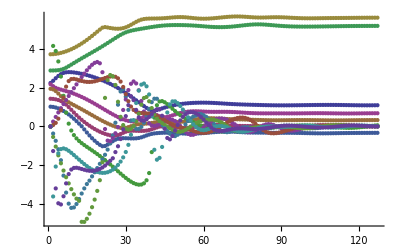

```mathematica
ListPlot[Transpose@soln]
```

```mathematica
Module[{},
Manipulate[
Show[
ring,
frame,
ball[soln⟦#2,1⟧&,0,a,randCol],
ball[soln⟦#2,2⟧&,0,a,col2],
ball[soln⟦#2,3⟧&,0,a,col3],
ball[soln⟦#2,4⟧&,0,a,col4],
ball[soln⟦#2,5⟧&,0,a,col5],
ball[soln⟦#2,6⟧&,0,a,col6],
ball[soln⟦#2,7⟧&,0,a,col7],
minotaurRK[soln⟦#3,#1⟧&,soln⟦#3,7+#1⟧&,1,0,a],
Boxed->True,
Axes->True,
AxesLabel->{"X","Y","Z"},
ViewPoint->{0,-∞,0},PlotRange->1.2,ImageSize->{400,400}],{{a,1,"animate"},1,Length@soln,1,ControlType->Animator,DisplayAllSteps->True,AppearanceElements->{"PlayPauseButton","FasterSlowerButtons"},AnimationRunning->True,AnimationRate->14},
{{a,1,"manual control"},1,Length@soln,1}]]
```

## Particles in a box

One-body Problem in the Plane

```mathematica
G=1;
```

Let the state vector be {x_1,y_1,OverDot[x_1],OverDot[y_1]}

Let c contain the coordinates of the fixed force center.

Compare to ArtCompSci

Compare with another demonstration, this one from http://www.artcompsci.org/ (the medium-size document, school series, Volume 1)

## EulerStep

```mathematica
eulerStep[ψ_,ϕ_,t_,dt_]:=Module[{dtk1=dt ϕ[ψ,t].ψ},ψ+dtk1]
```

The gravs matrix is

```mathematica
gravsMat[ψ_,c_,m1_,m2_]:=Module[{rCubed=EuclideanDistance[{ψ⟦1⟧,ψ⟦2⟧},c]^3},
{(* velocity section *)
{0,0,1,0},{0,0,0,1},
(* acceleration section *)
{G m1 m2 If[ψ⟦1⟧≠0,(c⟦1⟧-ψ⟦1⟧)/(ψ⟦1⟧rCubed),0],0,0,0},
{0,G m1 m2 If[ψ⟦2⟧≠0,(c⟦2⟧-ψ⟦2⟧)/(ψ⟦2⟧rCubed),0],0,0}}   ]
```

```mathematica
takeEveryNth[l_List,n_Integer]:=Table[l⟦i⟧,{i,1,Length[l],n}]
```

```mathematica
run[algo_,nStepsExp_,init_]:=takeEveryNth[
Module[{
dt=0.01/10^(nStepsExp-3), (* time step *)
t0=0., (* start time *)
tN=10., (* end time *)
ϕ}, (* function of q and t that returns a matrix in proper form *)
ϕ=Function[{q,t},gravsMat[q,{0,0},1,1]];
FoldList[
algo[#1,ϕ,#2,dt]&,(* calculate one step *)
init,(* initial state *)
Range[t0,tN,dt]]],10^(nStepsExp-3)]
```

```mathematica
(Timing[gravsSol=run[eulerStep,3,{1,0,0,1}]]⟦1⟧//ToString)<>" seconds to solve."
```

0.078 seconds to solve.

```mathematica
Length@gravsSol
```

1002

```mathematica
Take[gravsSol,5]~Join~{{"-","-","-","-"}}~Join~Take[gravsSol,-5]
```

(1 | 0 | 0 | 1
1 | 0.01 | -0.01 | 1
0.9999 | 0.02 | -0.0199985 | 0.9999
0.9997 | 0.029999 | -0.0299945 | 0.9997
0.9994 | 0.039996 | -0.039987 | 0.9994
- | - | - | -
-0.973257 | 0.632129 | -0.528172 | -0.768568
-0.978538 | 0.624443 | -0.521946 | -0.772612
-0.983758 | 0.616717 | -0.51569 | -0.776604
-0.988915 | 0.608951 | -0.509405 | -0.780544
-0.994009 | 0.601145 | -0.503092 | -0.784432)

```mathematica
showSol[g_,r_]:=ListPlot[Transpose[{g⟦All,1⟧,g⟦All,2⟧}],PlotRange->r,AspectRatio->1,Frame->True]
```

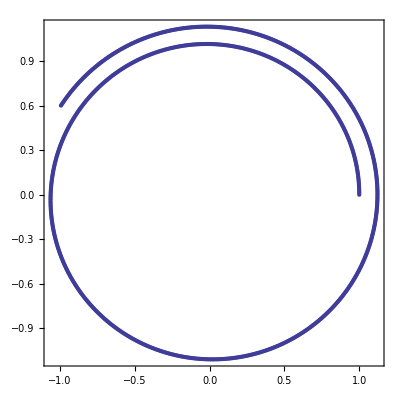

```mathematica
showSol[gravsSol,1.5]
```

Bingo! gaining energy, just like figure 20 (or 7.3 in the pdf version) in http://www.artcompsci.org/kali/pub/msa/title.html

Time to solve: 0.078

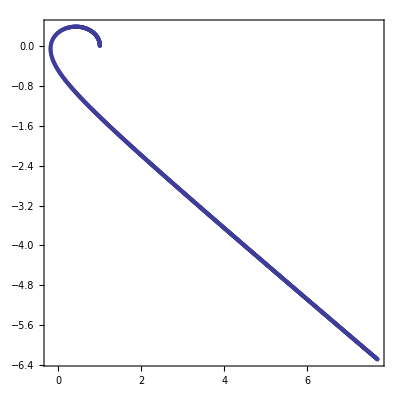

```mathematica
Module[{r=Timing@run[eulerStep,3,{1,0,0,0.5}]},
Print["Time to solve: "<>ToString@r⟦1⟧];showSol[r⟦2⟧,8]]
```

Time to solve: 0.671

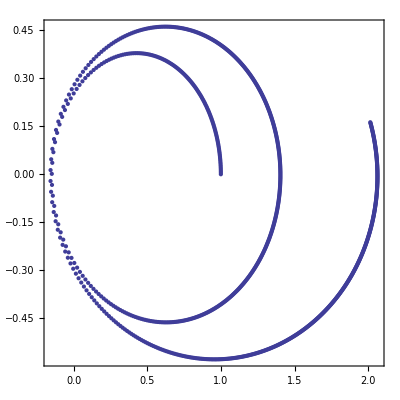

```mathematica
Module[{r=Timing@run[eulerStep,4,{1,0,0,0.5}]},
Print["Time to solve: "<>ToString@r⟦1⟧];showSol[r⟦2⟧,3]]
```

Here's the web site's figure 21 http://www.artcompsci.org/kali/pub/msa/ch08.html

Time to solve: 0.702

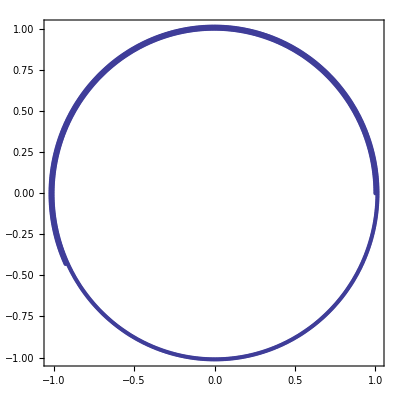

```mathematica
Module[{r=Timing@run[eulerStep,4,{1,0,0,1}]},
Print["Time to solve: "<>ToString@r⟦1⟧];showSol[r⟦2⟧,3/2]]
```

Time to solve: 6.848

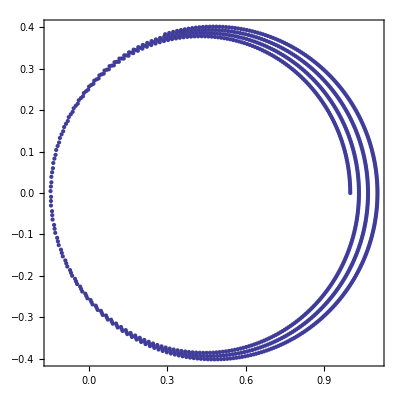

```mathematica
Module[{r=Timing@run[eulerStep,5,{1,0,0,0.5}]},
Print["Time to solve: "<>ToString@r⟦1⟧];showSol[r⟦2⟧,3/2]]
```

```mathematica
(Timing[gravsSol=run[eulerStep,6,{1,0,0,0.5}]]⟦1⟧//ToString)<>" seconds to solve."
```

68.796 seconds to solve.

Here's the web site's figure 25 http://www.artcompsci.org/kali/pub/msa/ch08.html

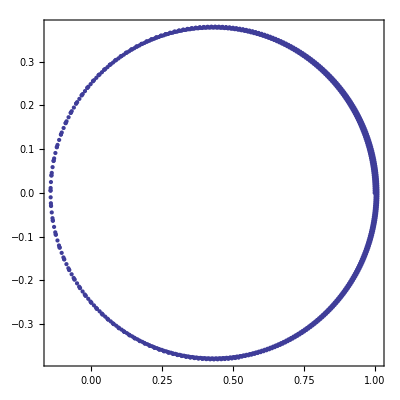

```mathematica
showSol[gravsSol,3/2]
```

Compare the last line of the following to the last line of page 109.

```mathematica
Take[gravsSol,-3]
```

(0.496147 | -0.378819 | 1.21129 | 0.0849254
0.508159 | -0.377893 | 1.19109 | 0.100149
0.519971 | -0.376818 | 1.17127 | 0.114701)

9.5 From One Body to Two Bodies (following artcompsci)

Imitate the artcompsci idea to some extent.

```mathematica
print2[m1_,m2_,x_,y_,vx_,vy_]:=(* ignoring z and vz *)
With[{mfrac1=m1/(m1+m2),mfrac2=m2/(m1+m2)},
{{-mfrac2 x,-mfrac2 y,-mfrac2 vx,-mfrac2 vy},
{mfrac1 x,mfrac1 y,mfrac1 vx,mfrac1 vy}}]
```

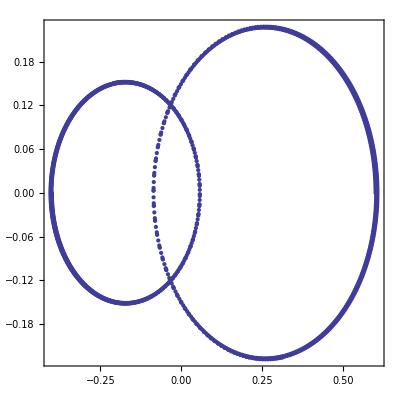

```mathematica
showSol[Flatten[
Map[
Function[ψ,print2[0.6,1-0.6,ψ⟦1⟧,ψ⟦2⟧,ψ⟦3⟧,ψ⟦4⟧]],
gravsSol],
1],
0.8]
```

Page 115 (section 10.1 of artcompsci)

## ModifiedEulerStep

```mathematica
modifiedEulerStep[ψ0_,ϕ_,t_,dt_]:=Module[
{ψ1,ψ2},
ψ1=ψ0+dt ϕ[ψ0,t].ψ0;
ψ2=ψ1+dt ϕ[ψ1,t+dt].ψ1;
(* return *) (ψ0+ψ2)/2]
```

Time to solve: 1.872

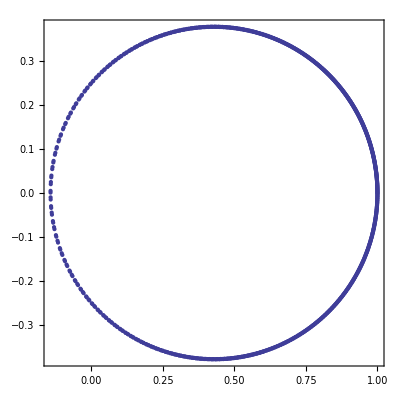

```mathematica
Module[{r=Timing@run[modifiedEulerStep,4,{1,0,0,0.5}]},
Print["Time to solve: "<>ToString@r⟦1⟧];showSol[r⟦2⟧,3/2]]
```

### Is our scheme broken?

Since we divide out by ψ and not by c-ψ, that is, the recentered coordinates, the gravs mat may be incorrect for centers other than {0,0}.

```mathematica
run2[algo_,nStepsExp_,init_]:=takeEveryNth[
Module[{
dt=0.01/10^(nStepsExp-3), (* time step *)
t0=0., (* start time *)
tN=10., (* end time *)
ϕ}, (* function of q and t that returns a matrix in proper form *)
ϕ=Function[{q,t},gravsMat[q,{-0.5,.5},1,1]];
FoldList[
algo[#1,ϕ,#2,dt]&,(* calculate one step *)
init,(* initial state *)
Range[t0,tN,dt]]],10^(nStepsExp-3)]
```

Time to solve: 1.528

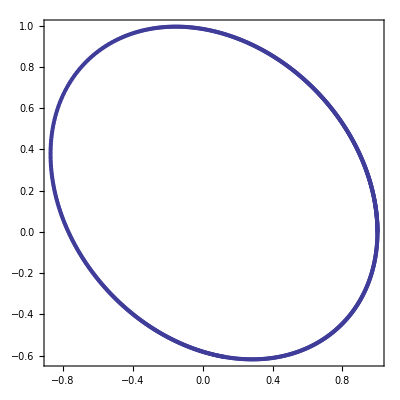

```mathematica
Module[{r=Timing@run2[modifiedEulerStep,4,{1,0,0,0.5}]},
Print["Time to solve: "<>ToString@r⟦1⟧];showSol[r⟦2⟧,3/2]]
```

It looks ok, but now this requires explanation. The position-components of the state vector are zero when the plot crosses either of the axes. At that point, the gravs matrix returns zero for acceleration. That's not right. It could be that the strange perturbation is small enough not to matter

### This is artcompsci's Figure 10.6

Time to solve: 0.156

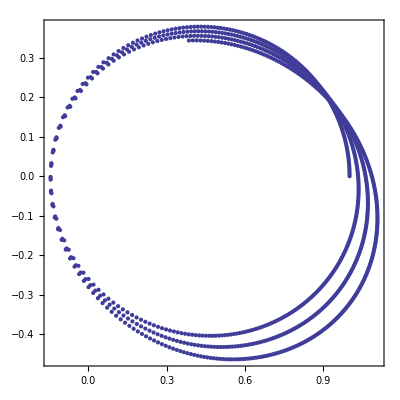

```mathematica
Module[{r=Timing@run[modifiedEulerStep,3,{1,0,0,0.5}]},
Print["Time to solve: "<>ToString@r⟦1⟧];showSol[r⟦2⟧,3/2]]
```

## LeapfrogStep

Must create a modified matrix, one that depends on dt. Generalized integration may have to be refactored so that the matrix takes t (for time-dependent functions) and dt (for step-size-dependent integration schemes) as arguments.

```mathematica
leapfrogGravsMat[ψ0_,dt_,c_,m1_,m2_]:=Module[{
r30=EuclideanDistance[{ψ0⟦1⟧,ψ0⟦2⟧},c]^3,
a10,a20,
ψ1,r31,a11,a21},
a10=G m1 m2 If[ψ0⟦1⟧≠0,(c⟦1⟧-ψ0⟦1⟧)/(ψ0⟦1⟧r30),0];
a20=G m1 m2 If[ψ0⟦2⟧≠0,(c⟦2⟧-ψ0⟦2⟧)/(ψ0⟦2⟧r30),0];
{(* velocity section *)
{0,0,1+(a10 dt)/2,0},
{0,0,0,1+(a20 dt)/2},
(* acceleration section *)
{a10,0,0,0},
{0,a20,0,0}}   ]
```

```mathematica
leapfrogStep[ψ0_,ϕ_,t_,dt_]:=Module[
{va1,ψ1,ψ2,extraMat},
va1=ϕ[ψ0,t];
(* return *)0]
```

```mathematica
Module[{r=Timing@run[modifiedEulerStep,4,{1,0,0,0.5}]},
Print["Time to solve: "<>ToString@r⟦1⟧];showSol[r⟦2⟧,3/2]]
```

Time to solve: 1.872

-Graphics-

## Nicer Display

```mathematica
Module[{rg={{-10,-10},{10,10}}},
Manipulate[
Show[
ball2[u,{randCol}],
ball2[b],
PlotRange->10,
AxesLabel->{"X","Y","Z"},
Axes->True,
Boxed->True,
ViewPoint->{0,0,∞}],
{{u,{0,0},"foo"},Sequence@@rg},
{{b,{4,7},"bar"},Sequence@@rg},
ControlPlacement->Left
]]
```